# Метод на хордите

Задача: Дадено ни е уравнението:
x^4-12 x^3 +77sinx- 32 = 0
1. Да се визуализира функцията
2. Да се определи броя на корените
3. Да се локализира един от тях 
4. Да се уточни локализирания корен по метода на хордите - проверка на условията на метода, избор на начално приближение и постоянна точка, итерациите
5. Оценка на грешката
6. Колко итерации биха били необходими за достигане на точност 0.0001 по метода на разполовяването за избрания по време на локализацията интервал?
7. Да се направи сравнение на ефективността на метода на хордите и метода на разполовяването

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32
```

## 1. Да се визуализира функцията

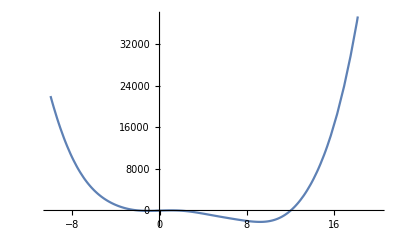

```mathematica
Plot[f[x],{x,-10,20}]
```

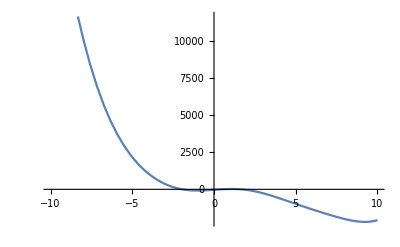

```mathematica
Plot[f[x],{x,-10,10}]
```

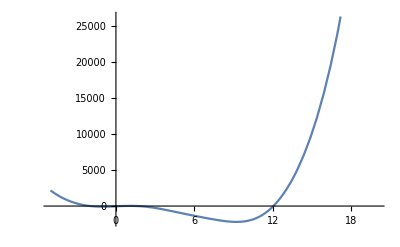

```mathematica
Plot[f[x],{x,-5,20}]
```

## 2. Да се определи броя на корените

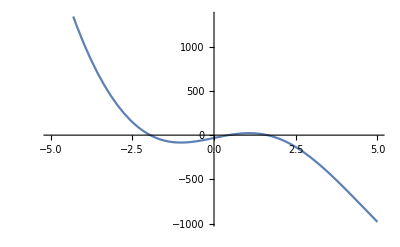

```mathematica
Plot[f[x],{x,-5,5}]
```

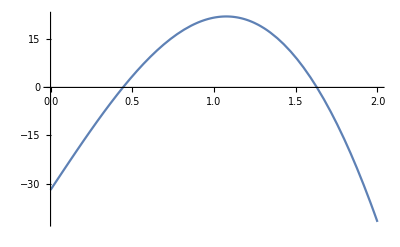

```mathematica
Plot[f[x],{x,0,2}]
```

## 3. Да се локализира един от тях

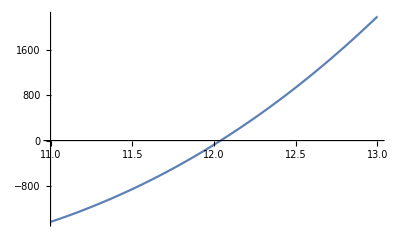

```mathematica
Plot[f[x],{x,11,13}]
```

```mathematica
f[11.]
```

-1440.

```mathematica
f[13.]
```

2197.35

Извод: 
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(11) = -1440 < 0
       f(13) = 2197.35.... > 0
       Функцията има различни знаци в двата края на разглеждания интервал [11; 13].
       Следователно от (1) и (2) следва, че в интервала [11; 13] функцията има поне един корен.

## 4. Да се уточни локализирания корен по метода на хордите

### проверка на условията на метода

#### Проверка знака на първата производна

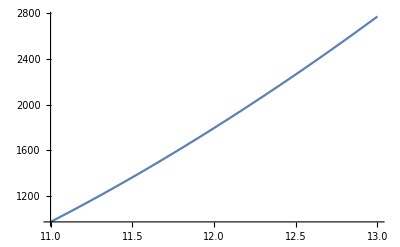

```mathematica
Plot[f'[x],{x,11,13}]
```

Извод: (1) Геометрично виждаме, че стойностите на първата производна в разглеждания интервал [11; 13] са между 1000 и 3000. Следователно f’(x) > 0 за x в интервала [11; 13] .

#### Проверка знака на втората производна

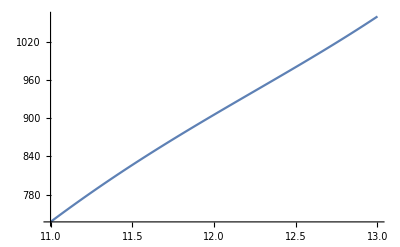

```mathematica
Plot[f''[x],{x,11,13}]
```

Извод: (2) Геометрично виждаме, че стойностите на втората производна в разглеждания интервал [11; 13] са между 700 и 1100. Следователно f’’(x) > 0 за x в интервала [11; 13] .

Следователно от (1) и (2) имаме изпълнение на условието за сходимост, че двете производни имат постоянен знак в разглеждания интервал [11; 13].

### избор на начално приближение и постоянна точка

според формулата от файла или условието на дъската

```mathematica
x0 = 11.
p = 13
```

11.

13

### итерациите

```mathematica
For[n = 1, n<=10, n++,
x1 = x0-f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", x1];
x0 = x1
]
```

n = 1 x_n = 11.7918

n = 2 x_n = 11.9885

n = 3 x_n = 12.0299

n = 4 x_n = 12.0384

n = 5 x_n = 12.04

n = 6 x_n = 12.0404

n = 7 x_n = 12.0405

n = 8 x_n = 12.0405

n = 9 x_n = 12.0405

n = 10 x_n = 12.0405

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32
a = 11.; b = 13;
x0 = a;
p = b;
For[n = 1, n<=10, n++,
x1 = x0-f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", SetPrecision[x1,15]];
x0 = x1
]
```

n = 1 x_n = 11.7917843548004

n = 2 x_n = 11.9884641553263

n = 3 x_n = 12.0299355504413

n = 4 x_n = 12.0383539848953

n = 5 x_n = 12.0400494736915

n = 6 x_n = 12.0403904051498

n = 7 x_n = 12.0404589382026

n = 8 x_n = 12.0404727136307

n = 9 x_n = 12.0404754825131

n = 10 x_n = 12.0404760390613

```mathematica
f[11.]
```

-1440.

```mathematica
11-1440/(1440+2197.35286183)*(11-13)
```

11.7918

#### определяне на постояннните величини

```mathematica
f[p]
```

2165+77 Sin[13]

```mathematica
f[13.]
```

2197.35

```mathematica
Plot[Abs[f'[x]],{x,11,13}]
```

-Graphics-

Извод: Максимума на абсолютната стойност на първата производна се достига в десния край, а минимума - в левия.

```mathematica
M1 = Abs[f'[13.]]
```

2773.87

```mathematica
m1 = Abs[f'[11.]]
```

968.341

```mathematica
R =(M1-m1)/m1
```

1.86456

#### окончателен код

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32
a = 11.; b = 13;
x0 = a;
p = b;
M1 = Abs[f'[13.]];m1 = Abs[f'[11.]];R =(M1-m1)/m1;
For[n = 1, n<=10, n++,
x1 = x0-f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", SetPrecision[x1,15], " f(x_n) = ", f[x1], " ε_n = ", eps = R*Abs[x1-x0]];
x0 = x1
]
```

n = 1 x_n = 11.7917843548004 f(x_n) = -427.246 ε_n = 1.47633

n = 2 x_n = 11.9884641553263 f(x_n) = -93.9394 ε_n = 0.366722

n = 3 x_n = 12.0299355504413 f(x_n) = -19.2361 ε_n = 0.077326

n = 4 x_n = 12.0383539848953 f(x_n) = -3.88102 ε_n = 0.0156967

n = 5 x_n = 12.0400494736915 f(x_n) = -0.780679 ε_n = 0.00316135

n = 6 x_n = 12.0403904051498 f(x_n) = -0.156941 ε_n = 0.000635688

n = 7 x_n = 12.0404589382026 f(x_n) = -0.0315462 ε_n = 0.000127784

n = 8 x_n = 12.0404727136307 f(x_n) = -0.00634086 ε_n = 0.0000256852

n = 9 x_n = 12.0404754825131 f(x_n) = -0.00127452 ε_n = 5.16276×10^-6

n = 10 x_n = 12.0404760390613 f(x_n) = -0.00025618 ε_n = 1.03772×10^-6

със стоп-критерий при достигане на предварително зададена точност

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32
a = 11.; b = 13;
x0 = a;
p = b;
M1 = Abs[f'[13.]];m1 = Abs[f'[11.]];R =(M1-m1)/m1;
epszad = 0.0001;
eps = 1;
Print["n = ", 0, " x_n = ", SetPrecision[x0,15], " f(x_n) = ", f[x0]];
For[n = 1, eps>epszad, n++,
x1 = x0-f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ", n, " x_n = ", SetPrecision[x1,15], " f(x_n) = ", f[x1], " ε_n = ", eps = R*Abs[x1-x0]];
x0 = x1
]
```

n = 0 x_n = 11. f(x_n) = -1440.

n = 1 x_n = 11.7917843548004 f(x_n) = -427.246 ε_n = 1.47633

n = 2 x_n = 11.9884641553263 f(x_n) = -93.9394 ε_n = 0.366722

n = 3 x_n = 12.0299355504413 f(x_n) = -19.2361 ε_n = 0.077326

n = 4 x_n = 12.0383539848953 f(x_n) = -3.88102 ε_n = 0.0156967

n = 5 x_n = 12.0400494736915 f(x_n) = -0.780679 ε_n = 0.00316135

n = 6 x_n = 12.0403904051498 f(x_n) = -0.156941 ε_n = 0.000635688

n = 7 x_n = 12.0404589382026 f(x_n) = -0.0315462 ε_n = 0.000127784

n = 8 x_n = 12.0404727136307 f(x_n) = -0.00634086 ε_n = 0.0000256852

по разполовяване

```mathematica
Log2[(13-11)/0.0001]-1
```

13.2877

Извод: За достигане на същата точност са необходими 14 итерации. А с метод на хордите - 8 итерации. Следователно методът на хордите е по-ефективен.